```mathematica
f1[t1_,t2_]:=Sin[t1]Sin[t2]
```

```mathematica
f2[t1_,t2_]:=Cos[t1]
```

```mathematica
f3[t1_,t2_]:=Cos[t2]
```

```mathematica
Plot3D[{f1[t1,t2]+f2[t1,t2]+f3[t1,t2]},{t1,-Pi,Pi},{t2,-Pi,Pi}]
```

-Graphics3D-

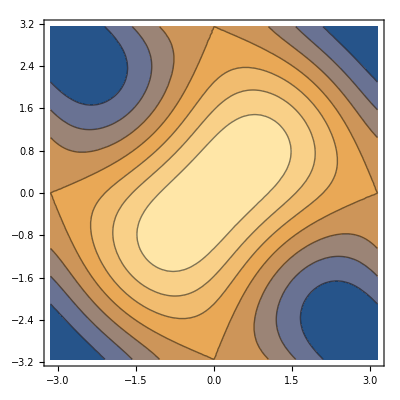

```mathematica
ContourPlot[{f1[t1,t2]+f2[t1,t2]+f3[t1,t2]},{t1,-Pi,Pi},{t2,-Pi,Pi}]
```

```mathematica
N[ArcTan[-2Pi]]
```

-1.41297

```mathematica
Cos[ArcTan[-2Pi]]
```

1/(√(1+4 π^2))

```mathematica
Sin[ArcTan[-2Pi]]
```

-(2 π)/(√(1+4 π^2))

```mathematica
Animate[Plot[{Sin[x],Sin[a]+Cos[a](x-a),Sin[a]+Cos[a](x-a)-Sin[a]/2(x-a)^2,Sin[a]+Cos[a](x-a)-Sin[a]/2(x-a)^2-Cos[a]/6(x-a)^3},{x,-2Pi,4Pi},AspectRatio->1,PlotRange->2,GridLines->{{a+2Pi},{}}],{a,-3Pi/4,3Pi/2,Pi/1000},AnimationRunning->False,AnimationDirection->ForwardBackward,DefaultDuration->100]
```

```mathematica
Animate[Plot[{Sin[x],Sin[a]+Cos[a] (x-a),Sin[a]+Cos[a] (x-a)-1/2 Sin[a] (x-a)^2,Sin[a]+Cos[a] (x-a)-1/2 Sin[a] (x-a)^2-1/6 Cos[a] (x-a)^3},{x,-2 π,4 π},AspectRatio->1,PlotRange->2,GridLines->{{a+2 π},{}}],{a,-(3 π)/4,(3 π)/2,π/1000},DefaultDuration->100,AnimationDirection->ForwardBackward,AnimationRunning->False,DisplayAllSteps->True]
```

```mathematica
Animate[Plot[{Sin[x],Sin[a]+Cos[a] (x-a),Sin[a]+Cos[a] (x-a)-1/2 Sin[a] (x-a)^2,Sin[a]+Cos[a] (x-a)-1/2 Sin[a] (x-a)^2-1/6 Cos[a] (x-a)^3,Sin[a]+Cos[a] (x-a)-1/2 Sin[a] (x-a)^2-1/6 Cos[a] (x-a)^3+1/24Sin[a](x-a)^4},{x,-2 π,4 π},AspectRatio->1,PlotRange->2,GridLines->{{a+2 π,a-2Pi},{}}],{a,-1/4 (3 π),(3 π)/2,π/1000},DefaultDuration->100,AnimationDirection->ForwardBackward,AnimationRunning->False,DisplayAllSteps->True]
```

```mathematica
f1[x_,y_]:=((1-y)Sin[x]+y Cos[x])/Sqrt[1-2y+2y^2]
```

```mathematica
f2[x_,y_]:=Sin[x+y Pi/2]
```

```mathematica
Plot3D[{f1[x,y],f2[x,y]},{x,0,2Pi},{y,0,1},Mesh->None,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[{f1[x,y]-f2[x,y]},{x,0,2Pi},{y,0,1},PlotPoints->50]
```

-Graphics3D-